```mathematica
ToLine[x_]:=Graphics[Line[Table[Flatten[Position[Transpose[Reverse[x]],i]],{i,Length[x]^2}]]]
ToLine[({{1, 2}, {3, 4}})]
```

-Graphics-

```mathematica
({{1, 2}, {4, 3}})
({{1, 2, 8, 5}, {4, 3, 7, 6}, {14, 15, 11, 12}, {13, 16, 10, 9}})
```

{{1,2},{4,3}}

{{1,2,8,5},{4,3,7,6},{14,15,11,12},{13,16,10,9}}

{{1,1,1},{2,1,2},{8,1,3},{5,1,4},{29,1,5},{30,1,6},{20,1,7},{17,1,8},{4,2,1},{3,2,2},{7,2,3},{6,2,4},{31,2,5},{32,2,6},{19,2,7},{18,2,8},{14,3,1},{15,3,2},{11,3,3},{12,3,4},{26,3,5},{27,3,6},{23,3,7},{24,3,8},{13,4,1},{16,4,2},{10,4,3},{9,4,4},{25,4,5},{28,4,6},{22,4,7},{21,4,8},{53,5,1},{54,5,2},{60,5,3},{57,5,4},{41,5,5},{42,5,6},{48,5,7},{45,5,8},{56,6,1},{55,6,2},{59,6,3},{58,6,4},{44,6,5},{43,6,6},{47,6,7},{46,6,8},{50,7,1},{51,7,2},{63,7,3},{64,7,4},{38,7,5},{39,7,6},{35,7,7},{36,7,8},{49,8,1},{52,8,2},{62,8,3},{61,8,4},{37,8,5},{40,8,6},{34,8,7},{33,8,8}}

{{1,1,1},{2,1,2},{3,2,2},{4,2,1},{5,1,4},{6,2,4},{7,2,3},{8,1,3},{9,4,4},{10,4,3},{11,3,3},{12,3,4},{13,4,1},{14,3,1},{15,3,2},{16,4,2},{17,1,8},{18,2,8},{19,2,7},{20,1,7},{21,4,8},{22,4,7},{23,3,7},{24,3,8},{25,4,5},{26,3,5},{27,3,6},{28,4,6},{29,1,5},{30,1,6},{31,2,5},{32,2,6},{33,8,8},{34,8,7},{35,7,7},{36,7,8},{37,8,5},{38,7,5},{39,7,6},{40,8,6},{41,5,5},{42,5,6},{43,6,6},{44,6,5},{45,5,8},{46,6,8},{47,6,7},{48,5,7},{49,8,1},{50,7,1},{51,7,2},{52,8,2},{53,5,1},{54,5,2},{55,6,2},{56,6,1},{57,5,4},{58,6,4},{59,6,3},{60,5,3},{61,8,4},{62,8,3},{63,7,3},{64,7,4}}

{{1,1},{1,2},{2,2},{2,1},{1,4},{2,4},{2,3},{1,3},{4,4},{4,3},{3,3},{3,4},{4,1},{3,1},{3,2},{4,2},{1,8},{2,8},{2,7},{1,7},{4,8},{4,7},{3,7},{3,8},{4,5},{3,5},{3,6},{4,6},{1,5},{1,6},{2,5},{2,6},{8,8},{8,7},{7,7},{7,8},{8,5},{7,5},{7,6},{8,6},{5,5},{5,6},{6,6},{6,5},{5,8},{6,8},{6,7},{5,7},{8,1},{7,1},{7,2},{8,2},{5,1},{5,2},{6,2},{6,1},{5,4},{6,4},{6,3},{5,3},{8,4},{8,3},{7,3},{7,4}}

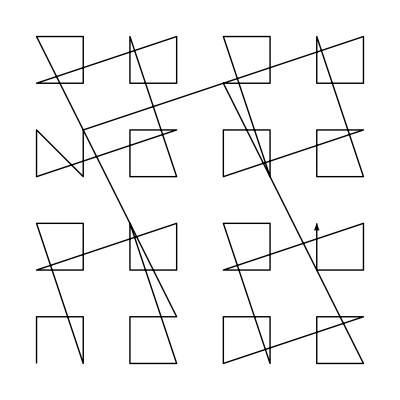

{{0,1},{1,0},{0,-1},{-1,3},{1,0},{0,-1},{-1,0},{3,1},{0,-1},{-1,0},{0,1},{1,-3},{-1,0},{0,1},{1,0},{-3,6},{1,0},{0,-1},{-1,0},{3,1},{0,-1},{-1,0},{0,1},{1,-3},{-1,0},{0,1},{1,0},{-3,-1},{0,1},{1,-1},{0,1},{6,2},{0,-1},{-1,0},{0,1},{1,-3},{-1,0},{0,1},{1,0},{-3,-1},{0,1},{1,0},{0,-1},{-1,3},{1,0},{0,-1},{-1,0},{3,-6},{-1,0},{0,1},{1,0},{-3,-1},{0,1},{1,0},{0,-1},{-1,3},{1,0},{0,-1},{-1,0},{3,1},{0,-1},{-1,0},{0,1}}

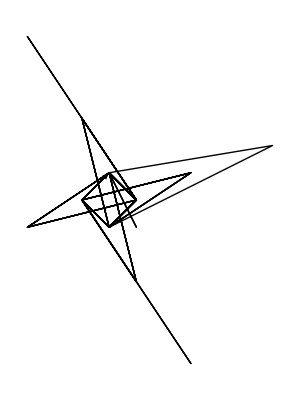

```mathematica
sq=({{1, 2, 8, 5, 29, 30, 20, 17}, {4, 3, 7, 6, 31, 32, 19, 18}, {14, 15, 11, 12, 26, 27, 23, 24}, {13, 16, 10, 9, 25, 28, 22, 21}, {53, 54, 60, 57, 41, 42, 48, 45}, {56, 55, 59, 58, 44, 43, 47, 46}, {50, 51, 63, 64, 38, 39, 35, 36}, {49, 52, 62, 61, 37, 40, 34, 33}});
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3]
ord=Sort[%,#1[[1]]<#2[[1]]&]
cut[x_]:=Drop[x,1]
ct=Map[cut,ord]
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}]
Graphics[Arrow[vectors]]
```

```mathematica
q=Partition[Table[i,{i,1,16}],4];
q//MatrixForm
```

(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12
13 | 14 | 15 | 16)

```mathematica
rt[x_]:=Transpose[Reverse[x]]
rt[q]//MatrixForm
rt[rt[q]]//MatrixForm
```

(13 | 9 | 5 | 1
14 | 10 | 6 | 2
15 | 11 | 7 | 3
16 | 12 | 8 | 4)

(16 | 15 | 14 | 13
12 | 11 | 10 | 9
8 | 7 | 6 | 5
4 | 3 | 2 | 1)

```mathematica
ArrayFlatten[({{({{1, 2}, {3, 4}}), 4+({{4, 1}, {3, 2}})}, {12+({{2, 3}, {1, 4}}), 8+({{3, 4}, {2, 1}})}})]//MatrixForm
```

(1 | 2 | 8 | 5
3 | 4 | 7 | 6
14 | 15 | 11 | 12
13 | 16 | 10 | 9)

```mathematica
rot[x_]:=Transpose[Reverse[x]]
fa[x_]:=ArrayFlatten[({{x, (Length[x])^2+rot[x]}, {3(Length[x])^2+rot[rot[rot[x]]], 2(Length[x])^2+rot[rot[x]]}})]
F[x_]:=Nest[fa,({{1, 2}, {4, 3}}),x]
```

```mathematica
fa[({{1, 2}, {4, 3}})]//MatrixForm
```

(1 | 2 | 8 | 5
4 | 3 | 7 | 6
14 | 15 | 11 | 12
13 | 16 | 10 | 9)

```mathematica
F[2]//MatrixForm
```

(1 | 2 | 8 | 5 | 29 | 30 | 20 | 17
4 | 3 | 7 | 6 | 32 | 31 | 19 | 18
14 | 15 | 11 | 12 | 26 | 27 | 23 | 24
13 | 16 | 10 | 9 | 25 | 28 | 22 | 21
53 | 54 | 60 | 57 | 41 | 42 | 48 | 45
56 | 55 | 59 | 58 | 44 | 43 | 47 | 46
50 | 51 | 63 | 64 | 38 | 39 | 35 | 36
49 | 52 | 62 | 61 | 37 | 40 | 34 | 33)

{{1,1,1},{2,1,2},{8,1,3},{5,1,4},{29,1,5},{30,1,6},{20,1,7},{17,1,8},{113,1,9},{114,1,10},{120,1,11},{117,1,12},{77,1,13},{78,1,14},{68,1,15},{65,1,16},{449,1,17},{450,1,18},{456,1,19},{453,1,20},{477,1,21},{478,1,22},{468,1,23},{465,1,24},{305,1,25},{306,1,26},{312,1,27},{309,1,28},{269,1,29},{270,1,30},{260,1,31},{257,1,32},«16321»,{8452,128,98},{8462,128,99},{8461,128,100},{8501,128,101},{8504,128,102},{8498,128,103},{8497,128,104},{8657,128,105},{8660,128,106},{8670,128,107},{8669,128,108},{8645,128,109},{8648,128,110},{8642,128,111},{8641,128,112},{8257,128,113},{8260,128,114},{8270,128,115},{8269,128,116},{8309,128,117},{8312,128,118},{8306,128,119},{8305,128,120},{8209,128,121},{8212,128,122},{8222,128,123},{8221,128,124},{8197,128,125},{8200,128,126},{8194,128,127},{8193,128,128}}

{{1,1,1},{2,1,2},{3,2,2},{4,2,1},{5,1,4},{6,2,4},{7,2,3},{8,1,3},{9,4,4},{10,4,3},{11,3,3},{12,3,4},{13,4,1},{14,3,1},{15,3,2},{16,4,2},{17,1,8},{18,2,8},{19,2,7},{20,1,7},{21,4,8},{22,4,7},{23,3,7},{24,3,8},{25,4,5},{26,3,5},{27,3,6},{28,4,6},{29,1,5},{30,1,6},{31,2,6},{32,2,5},{33,8,8},{34,8,7},«16317»,{16352,98,53},{16353,104,56},{16354,104,55},{16355,103,55},{16356,103,56},{16357,104,53},{16358,103,53},{16359,103,54},{16360,104,54},{16361,101,53},{16362,101,54},{16363,102,54},{16364,102,53},{16365,101,56},{16366,102,56},{16367,102,55},{16368,101,55},{16369,104,49},{16370,103,49},{16371,103,50},{16372,104,50},{16373,101,49},{16374,101,50},{16375,102,50},{16376,102,49},{16377,101,52},{16378,102,52},{16379,102,51},{16380,101,51},{16381,104,52},{16382,104,51},{16383,103,51},{16384,103,52}}

{{1,1},{1,2},{2,2},{2,1},{1,4},{2,4},{2,3},{1,3},{4,4},{4,3},{3,3},{3,4},{4,1},{3,1},{3,2},{4,2},{1,8},{2,8},{2,7},{1,7},{4,8},{4,7},{3,7},{3,8},{4,5},{3,5},{3,6},{4,6},{1,5},{1,6},{2,6},{2,5},{8,8},{8,7},{7,7},{7,8},{8,5},{7,5},{7,6},{8,6},{5,5},{5,6},{6,6},{6,5},{5,8},{6,8},{6,7},{5,7},{8,1},{7,1},{7,2},{8,2},{5,1},{5,2},«16276»,{99,51},{99,52},{100,49},{99,49},{99,50},{100,50},{97,56},{98,56},{98,55},{97,55},{100,56},{100,55},{99,55},{99,56},{100,53},{99,53},{99,54},{100,54},{97,53},{97,54},{98,54},{98,53},{104,56},{104,55},{103,55},{103,56},{104,53},{103,53},{103,54},{104,54},{101,53},{101,54},{102,54},{102,53},{101,56},{102,56},{102,55},{101,55},{104,49},{103,49},{103,50},{104,50},{101,49},{101,50},{102,50},{102,49},{101,52},{102,52},{102,51},{101,51},{104,52},{104,51},{103,51},{103,52}}

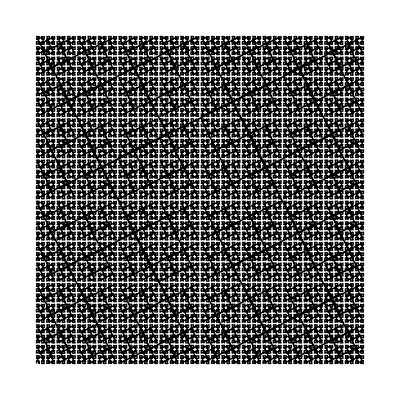

{{0,1},{1,0},{0,-1},{-1,3},{1,0},{0,-1},{-1,0},{3,1},{0,-1},{-1,0},{0,1},{1,-3},{-1,0},{0,1},{1,0},{-3,6},{1,0},{0,-1},{-1,0},{3,1},{0,-1},{-1,0},{0,1},{1,-3},{-1,0},{0,1},{1,0},{-3,-1},{0,1},{1,0},{0,-1},{6,3},{0,-1},{-1,0},{0,1},{1,-3},{-1,0},{0,1},{1,0},{-3,-1},{0,1},{1,0},{0,-1},{-1,3},{1,0},{0,-1},{-1,0},{3,-6},{-1,0},{0,1},{1,0},{-3,-1},{0,1},{1,0},{0,-1},{-1,3},{1,0},{0,-1},{-1,0},{3,1},«16263»,{-1,3},{1,0},{0,-1},{-1,0},{3,1},{0,-1},{-1,0},{0,1},{1,-3},{-1,0},{0,1},{1,0},{-3,6},{1,0},{0,-1},{-1,0},{3,1},{0,-1},{-1,0},{0,1},{1,-3},{-1,0},{0,1},{1,0},{-3,-1},{0,1},{1,0},{0,-1},{6,3},{0,-1},{-1,0},{0,1},{1,-3},{-1,0},{0,1},{1,0},{-3,-1},{0,1},{1,0},{0,-1},{-1,3},{1,0},{0,-1},{-1,0},{3,-6},{-1,0},{0,1},{1,0},{-3,-1},{0,1},{1,0},{0,-1},{-1,3},{1,0},{0,-1},{-1,0},{3,1},{0,-1},{-1,0},{0,1}}

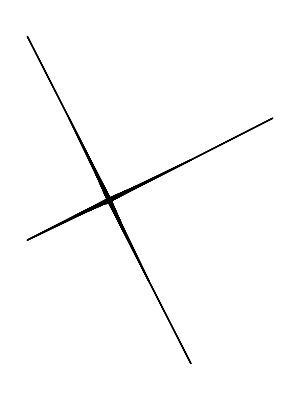

```mathematica
sq=F[6];
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3]
ord=Sort[%,#1[[1]]<#2[[1]]&]
cut[x_]:=Drop[x,1]
ct=Map[cut,ord]
Graphics[Line[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}]
Graphics[Arrow[vectors]]
```

```mathematica
print out with big paper
one night, four peorpl (one on each corner)
each smoke a clove and when done, put them out in gasoline on paper
and quartz underneath to transfer energy to quartz
1024->(too much?) a little bit more than we need/plenty (appx 10^9 J)
as fractal (lines)
```

```mathematica
rot[x_]:=Transpose[Reverse[x]]
fa[x_]:=ArrayFlatten[({{x, (Length[x])^2+rot[x]}, {3(Length[x])^2+rot[rot[rot[x]]], 2(Length[x])^2+rot[rot[x]]}})]
fb[x_]:=ArrayFlatten[({{x, 3(Length[x])^2+rot[rot[rot[x]]]}, {(Length[x])^2+rot[x], 2(Length[x])^2+rot[rot[x]]}})]
G[x_List]:=Apply[Composition,Table[Piecewise[{{fa, x[[i]]==1}, {fb, x[[i]]==0}}],{i,2,Length[x]}]][Piecewise[{{({{1, 2}, {4, 3}}), x[[1]]==1}, {({{1, 4}, {2, 3}}), x[[1]]==0}}]]
```

```mathematica
G[{1,0}]//MatrixForm
```

(1 | 2 | 14 | 15
4 | 3 | 13 | 16
8 | 5 | 11 | 12
7 | 6 | 10 | 9)

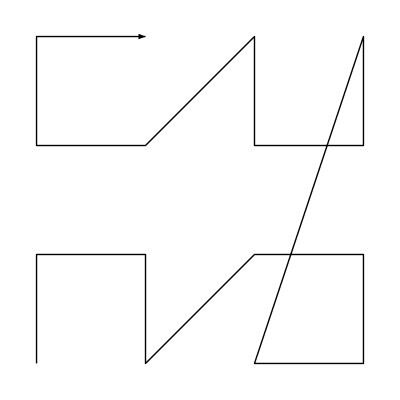

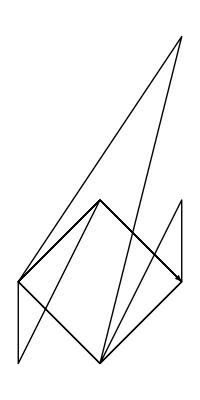

```mathematica
({{1, 2, 14, 15}, {4, 3, 13, 16}, {8, 5, 11, 12}, {7, 6, 10, 9}});
sq=%;
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3];
ord=Sort[%,#1[[1]]<#2[[1]]&];
cut[x_]:=Drop[x,1];
ct=Map[cut,ord];
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}];
Graphics[Arrow[vectors]]
```

```mathematica
w=1;
sq=G[IntegerDigits[w,2]];
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3];
ord=Sort[%,#1[[1]]<#2[[1]]&];
cut[x_]:=Drop[x,1];
ct=Map[cut,ord];
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}];
Graphics[Arrow[vectors]]
```

-Graphics-

-Graphics-

```mathematica
w=2;
sq=G[IntegerDigits[w,2]];
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3];
ord=Sort[%,#1[[1]]<#2[[1]]&];
cut[x_]:=Drop[x,1];
ct=Map[cut,ord];
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}];
Graphics[Arrow[vectors]]
```

-Graphics-

-Graphics-

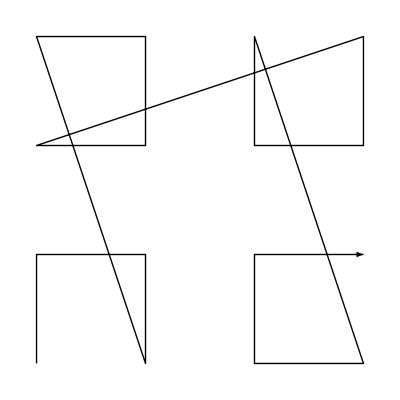

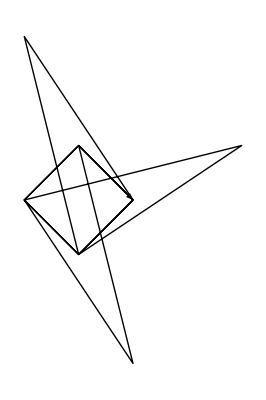

```mathematica
w=3;
sq=G[IntegerDigits[w,2]];
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3];
ord=Sort[%,#1[[1]]<#2[[1]]&];
cut[x_]:=Drop[x,1];
ct=Map[cut,ord];
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}];
Graphics[Arrow[vectors]]
```

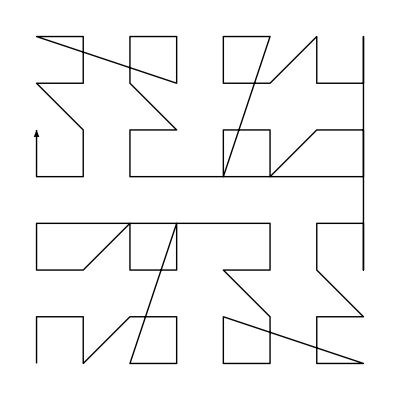

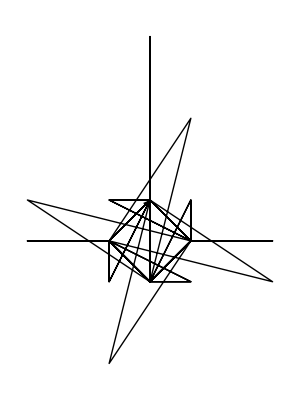

```mathematica
w=4;
sq=G[IntegerDigits[w,2]];
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3];
ord=Sort[%,#1[[1]]<#2[[1]]&];
cut[x_]:=Drop[x,1];
ct=Map[cut,ord];
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}];
Graphics[Arrow[vectors]]
```

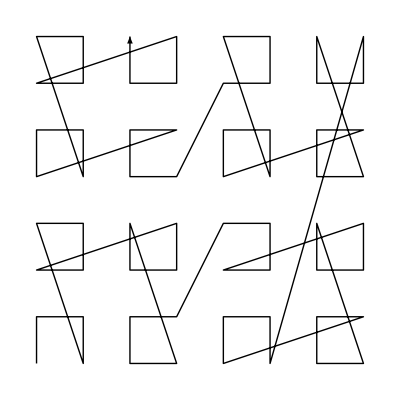

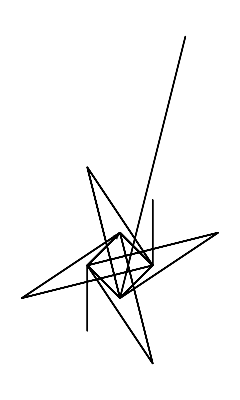

```mathematica
w=5;
sq=G[IntegerDigits[w,2]];
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3];
ord=Sort[%,#1[[1]]<#2[[1]]&];
cut[x_]:=Drop[x,1];
ct=Map[cut,ord];
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}];
Graphics[Arrow[vectors]]
```

127

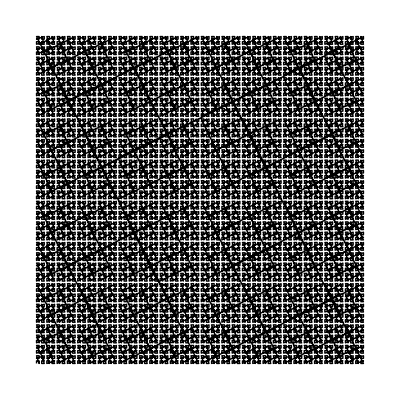

-Graphics-

```mathematica
w=RandomInteger[{1,255}]
sq=G[IntegerDigits[w,2]];
Partition[Flatten[Table[{sq[[i]][[j]],i,j},{i,1,Length[sq]},{j,1,Length[sq]}]],3];
ord=Sort[%,#1[[1]]<#2[[1]]&];
cut[x_]:=Drop[x,1];
ct=Map[cut,ord];
Graphics[Arrow[ct]]
vectors=Table[Drop[ord[[i+1]],1]-Drop[ord[[i]],1],{i,1,(Length[ord]-1)}];
Graphics[Arrow[vectors]]
```

```mathematica
(1)
({{1, 2}, {4, 3}})
({{1, 2, 3}, {8, 9, 4}, {7, 6, 5}})
({{1, 2, 8, 5}, {4, 3, 7, 6}, {14, 15, 11, 12}, {13, 16, 10, 9}})
({{1, 2, 3, 4, 5}, {16, 17, 18, 19, 6}, {15, 24, 25, 20, 7}, {14, 23, 22, 21, 8}, {13, 12, 11, 10, 9}})
({{1, 2, 8, 5, 11, 12}, {4, 3, 7, 6, 10, 9}, {30, 31, 33, 34, 14, 15}, {29, 32, 36, 35, 13, 16}, {27, 28, 24, 21, 17, 18}, {26, 25, 23, 22, 20, 19}})
({{1, 2, 3, 4, 5, 6, 7}, {24, 25, 26, 27, 28, 29, 8}, {23, 40, 41, 42, 43, 30, 9}, {22, 39, 48, 49, 44, 31, 10}, {21, 38, 47, 46, 45, 32, 11}, {20, 37, 36, 35, 34, 33, 12}, {19, 18, 17, 16, 15, 14, 13}})
({{1, 2, 8, 5, 29, 30, 20, 17}, {4, 3, 7, 6, 31, 32, 19, 18}, {14, 15, 11, 12, 26, 27, 23, 24}, {13, 16, 10, 9, 25, 28, 22, 21}, {53, 54, 60, 57, 41, 42, 48, 45}, {56, 55, 59, 58, 44, 43, 47, 46}, {50, 51, 63, 64, 38, 39, 35, 36}, {49, 52, 62, 61, 37, 40, 34, 33}})
({{1, 2, 3, 16, 17, 10, 23, 24, 25}, {8, 9, 4, 15, 18, 11, 22, 27, 26}, {7, 6, 5, 14, 13, 12, 21, 20, 19}, {66, 67, 68, 73, 74, 75, 30, 31, 32}, {65, 72, 69, 80, 81, 76, 29, 36, 33}, {64, 71, 70, 79, 78, 77, 28, 35, 34}, {59, 60, 61, 52, 53, 46, 37, 38, 39}, {58, 63, 62, 51, 54, 47, 44, 45, 40}, {57, 56, 55, 50, 49, 48, 43, 42, 41}})
```

```mathematica
make prime clockwise spiral generator
compose spirals
apply % according to prime factorization of √elements in matrix
```

```mathematica
new ToLine[matrix] from location function from within mathematica
```

```mathematica
({{1, 2}, {4, 3}})
({{1, 2, 3}, {8, 9, 4}, {7, 6, 5}})
({{1, 2, 3, 4, 5}, {16, 17, 18, 19, 6}, {15, 24, 25, 20, 7}, {14, 23, 22, 21, 8}, {13, 12, 11, 10, 9}})
```

```mathematica
spa[L_,x_]:=Join[{Table[i,{i,L}]},
Table[Join[{4L-3-i},ConstantArray[x,L-2],{L+i}],{i,1,L-2}],
{Table[3L-i,{i,2,L+1}]}]
```

```mathematica
spa[3]
```

{{1,2,3},{8,0,4},{7,6,5}}

```mathematica
sp[L_]:=Apply[Plus,Join[{spa[L,0]},Table[ArrayPad[∑_(j=0)^(i-1) (4(L-2j)-4)+spa[L-2i,-(∑_(j=0)^(i-1) (4(L-2j)-4))],i],{i,1,-3/2+L/2}],{ArrayPad[{{L^2}},(L-1)/2]}]]
```

```mathematica
sp[3]//MatrixForm
```

(1 | 2 | 3
8 | 9 | 4
7 | 6 | 5)

```mathematica
Mcomp[x_,y_]:=ArrayFlatten[Replace[x,Table[i->(i-1) Length[y]^2+Nest[rot,rot[rot[rot[y]]],i],{i,Length[x]^2}],{2}]]
```

```mathematica
Mcomp[({{1, 2}, {4, 3}}),({{1, 2}, {3, 4}})]//MatrixForm
ToLine[%]
```

(1 | 2 | 7 | 5
3 | 4 | 8 | 6
14 | 16 | 12 | 11
13 | 15 | 10 | 9)

-Graphics-

```mathematica
pl[x_,y_]:=x+y
dww[x_,f_]:=Piecewise[{{Table[f[x[[i]],x[[i+1]]],{i,1,Length[x],2}], Mod[Length[x],2]==0}, {Join[Table[f[x[[i]],x[[i+1]]],{i,1,Length[x]-1,2}],{Last[x]}], Mod[Length[x],2]==1}}]
ap2[x_,f_]:=Nest[dww[#,f]&,x,Ceiling[N[Log2[Length[x]],3]]]
ap2[{1,2,3,4,5,6,7,8,9,10,11},pl]
```

{66}

(1 | 2 | 8 | 5 | 27 | 28 | 17 | 18
4 | 3 | 7 | 6 | 26 | 25 | 20 | 19
11 | 12 | 14 | 15 | 30 | 31 | 24 | 21
10 | 9 | 13 | 16 | 29 | 32 | 23 | 22
56 | 53 | 62 | 63 | 46 | 47 | 43 | 44
55 | 54 | 61 | 64 | 45 | 48 | 42 | 41
49 | 50 | 59 | 60 | 40 | 37 | 33 | 34
52 | 51 | 58 | 57 | 39 | 38 | 36 | 35)

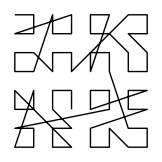

```mathematica
mcl[x_]:=Partition[Flatten[ap2[x,Mcomp]],Apply[Times,Map[Length[#]&,x]]]
mcl[{({{1, 2}, {4, 3}}),({{1, 2}, {3, 4}}),({{1, 2}, {4, 3}})}]//MatrixForm
ToLine[%]
```

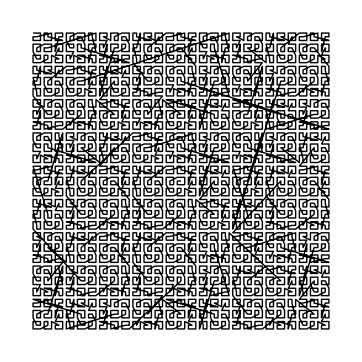

```mathematica
esp[x_]:=Piecewise[{{({{1, 2}, {4, 3}}), x==2}, {sp[x], x≠2}}]
aa[{x_,y_}]:=Table[x,{i,y}]
Spiral[x_]:=mcl[Map[esp,Flatten[Map[aa,FactorInteger[x]]]]]
ToLine[Spiral[81]]
```

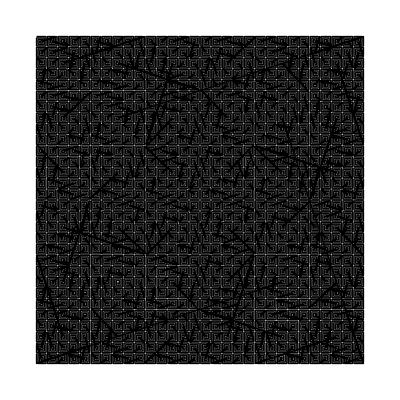

```mathematica
ToLine[Spiral[210]]
```

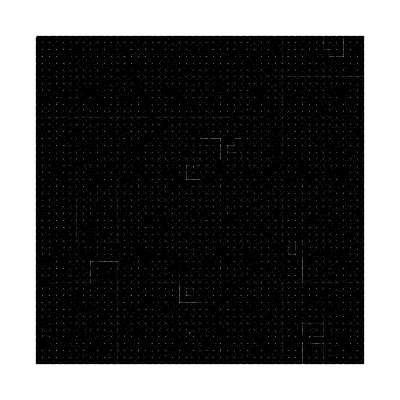

```mathematica
ToLine[Spiral[240]]
```

```mathematica
ToLine[Spiral[666]]
```

```mathematica
FactorInteger[666]
```

{{2,1},{3,2},{37,1}}

```mathematica
FactorInteger[777]
```

{{3,1},{7,1},{37,1}}

```mathematica
ToLine[Spiral[6^3]]
```

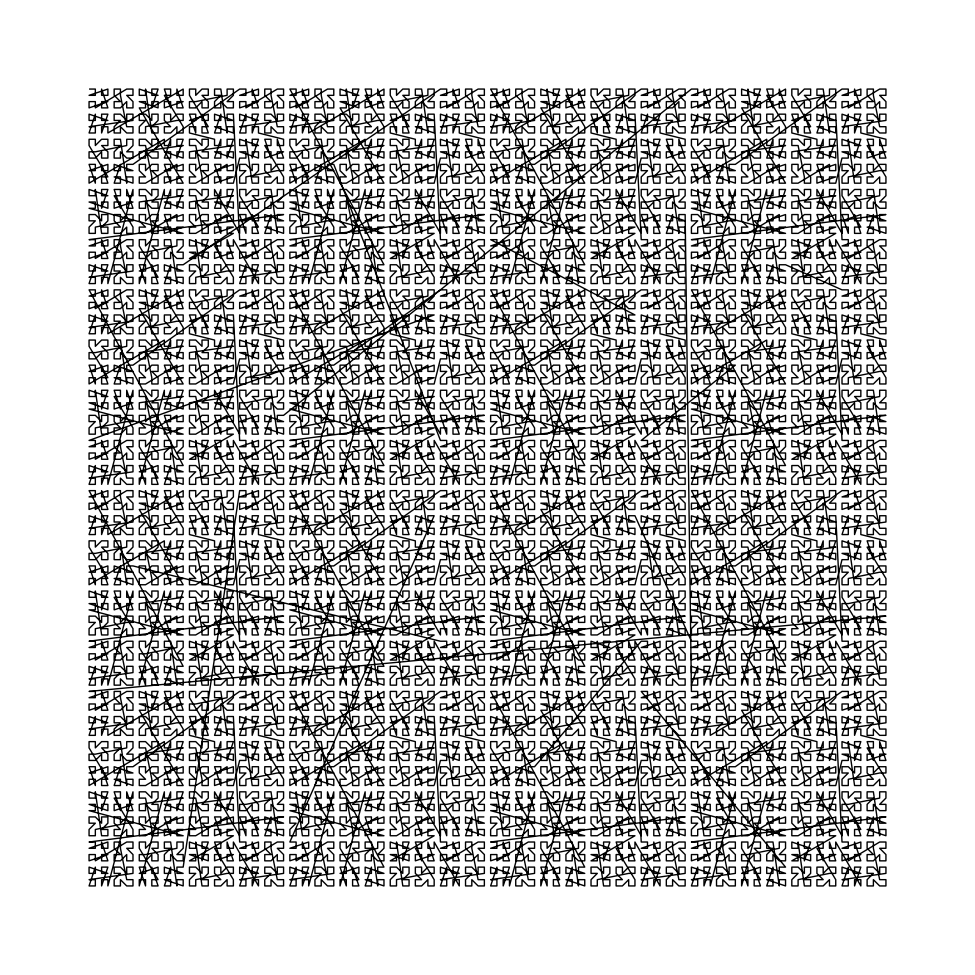

```mathematica
ToLine[Spiral[128]]
```

84

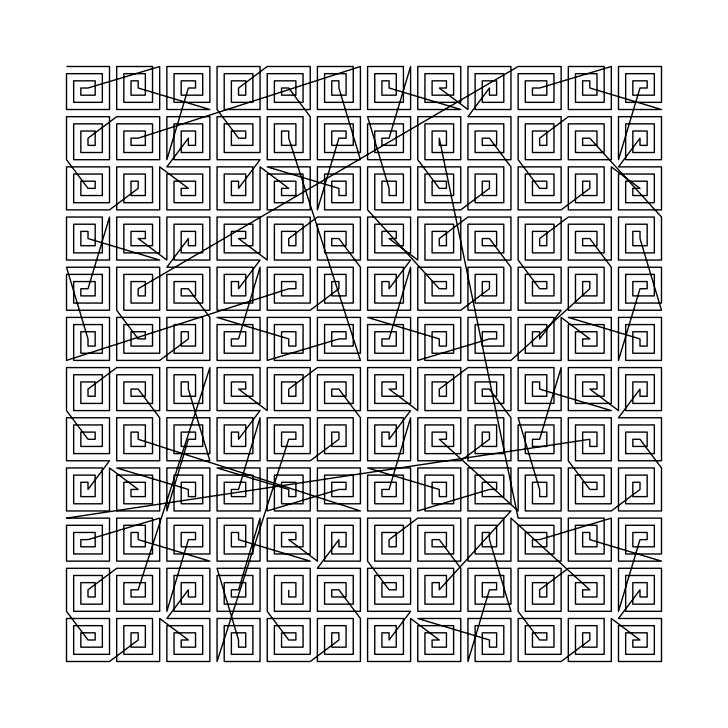

```mathematica
RandomInteger[{10,150}]
ToLine[Spiral[%]]
```

```mathematica
2 3 5 8
```

240

```mathematica
ToLine[Spiral[377]]
```

$Aborted

```mathematica
Map[Piecewise[{{1, PrimeQ[#]==True}, {0, True}}]&,({{1, 2}, {3, 4}}),{2}]
```

{{0,1},{1,0}}

```mathematica
dw=Spiral[256];
ToLine[dw]
ArrayPlot[Map[Piecewise[{{1, PrimeQ[#]==True}, {0, True}}]&,dw,{2}]]
```